# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to immunotherapy BNT162b2-scaled peak (1.405941416) from Peeters et al. 2021

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.405941416)*scalarsabove1
```

{1.40594,1.39664,1.38723,1.37772,1.36811,1.3584,1.34862,1.33876,1.32885,1.31888,1.30888,1.29885,1.28881,1.27877,1.26874,1.25872,1.24873,1.23877,1.22885,1.21898,1.20915,1.19937,1.18963,1.17995,1.17031,1.16072,1.15117,1.14166,1.13218,1.12272,1.11328,1.10386,1.09444,1.08498,1.0754,1.0657,1.05586,1.04587,1.03571,1.02537,1.01484,1.00412,0.993209,0.98211,0.9709,0.95969,0.94851,0.937385,0.926335,0.915376,0.904518,0.893767,0.883122,0.87258,0.862135,0.851775,0.841487,0.831254,0.821055,0.810867}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.40594,1.39664,1.38723,1.37772,1.36811,1.3584,1.34862,1.33876,1.32885,1.31888,1.30888,1.29885,1.28881,1.27877,1.26874,1.25872,1.24873,1.23877,1.22885,1.21898,1.20915,1.19937,1.18963,1.17995,1.17031,1.16072,1.15117,1.14166,1.13218,1.12272,1.11328,1.10386,1.09444,1.08498,1.0754,1.0657,1.05586,1.04587,1.03571,1.02537,1.01484,1.00412,0.993209,0.98211,0.9709,0.95969,0.94851,0.937385,0.926335,0.915376,0.904518,0.893767,0.883122,0.87258,0.862135,0.851775,0.841487,0.831254,0.821055,0.810867,0.80799,0.805126,0.802274,0.799435,0.796609,0.793795,0.790994,0.788205,0.785429,0.782665,0.779913,0.777173,0.774446,0.771731,0.769028,0.766337,0.763658,0.76099,0.758335,0.755692,0.75306,0.75044,0.747831,0.745235,0.742649,0.740076,0.737514,0.734963,0.732423,0.729895,0.727378,0.724872,0.722378,0.719894,0.717422,0.71496,0.71251,0.71007,0.707641,0.705223,0.702816,0.700419,0.698034,0.695658,0.693294,0.69094,0.688596,0.686263,0.68394,0.681627,0.679325,0.677033,0.674751,0.67248,0.670218,0.667967,0.665725,0.663494,0.661272,0.65906,0.656859,0.654666,0.652484,0.650312,0.648149,0.645995,0.643852,0.641717,0.639593,0.637478,0.635372,0.633275,0.631188,0.62911,0.627042,0.624982,0.622932,0.620891,0.618859,0.616836,0.614822,0.612817,0.610821,0.608834,0.606855,0.604886,0.602925,0.600973,0.599029,0.597094,0.595168,0.593251,0.591342,0.589441,0.587549,0.585665,0.58379,0.581923,0.580064,0.578214,0.576372,0.574538,0.572712,0.570894,0.569085,0.567283,0.56549,0.563704,0.561926,0.560157,0.558395,0.556641,0.554895,0.553156,0.551425,0.549702,0.547987,0.546279,0.544579,0.542887,0.541202,0.539524,0.537854,0.536192,0.534536,0.532889,0.531248,0.529615,0.527989,0.52637,0.524759,0.523154,0.521557,0.519967,0.518384,0.516808,0.515239,0.513677,0.512122,0.510574,0.509032,0.507498,0.50597,0.50445,0.502936,0.501428,0.499928,0.498434,0.496947,0.495466,0.493992,0.492525,0.491064,0.489609,0.488161,0.48672,0.485285,0.483856,0.482433,0.481017,0.479608,0.478204,0.476807,0.475416,0.474031,0.472652,0.47128,0.469913,0.468553,0.467199,0.46585,0.464508,0.463172,0.461841,0.460517,0.459198,0.457886,0.456579,0.455278,0.453983,0.452693,0.451409,0.450131,0.448859,0.447592,0.446331,0.445076,0.443826,0.442582,0.441343,0.44011,0.438882,0.437659,0.436443,0.435231,0.434025,0.432824,0.431629,0.430439,0.429254,0.428075,0.426901,0.425732,0.424568,0.423409,0.422256,0.421107,0.419964,0.418826,0.417693,0.416565,0.415442,0.414324,0.413211,0.412103,0.410999,0.409901,0.408808,0.407719,0.406636,0.405557,0.404483,0.403413,0.402349,0.401289,0.400234,0.399184,0.398138,0.397097,0.396061,0.395029,0.394002,0.392979,0.391961,0.390947,0.389938,0.388934,0.387934,0.386938,0.385947,0.38496,0.383977,0.382999,0.382026,0.381056,0.380091,0.379131,0.378174,0.377222,0.376274,0.37533,0.37439,0.373455,0.372524,0.371597,0.370674,0.369755,0.36884,0.367929,0.367023,0.36612,0.365222,0.364327,0.363436,0.36255,0.361667,0.360788,0.359913,0.359042,0.358175,0.357312,0.356452,0.355597,0.354745,0.353897,0.353053,0.352212,0.351376,0.350543,0.349713,0.348888,0.348066,0.347248,0.346433,0.345622,0.344814,0.344011,0.34321,0.342414,0.341621,0.340831,0.340045,0.339262,0.338483,0.337708,0.336935,0.336167,0.335401,0.334639,0.333881,0.333126,0.332374,0.331625,0.33088,0.330138,0.3294,0.328665,0.327933,0.327204,0.326478,0.325756,0.325037,0.324321,0.323609,0.322899,0.322193,0.32149,0.32079,0.320093,0.319399,0.318708,0.31802,0.317336,0.316654,0.315976,0.3153,0.314628,0.313958,0.313292,0.312628,0.311967,0.31131,0.310655,0.310003,0.309354,0.308708,0.308065,0.307425,0.306787,0.306152,0.305521,0.304892,0.304265,0.303642,0.303021,0.302403,0.301788,0.301176,0.300566,0.299959,0.299355,0.298753,0.298155,0.297558,0.296965,0.296374,0.295785,0.2952,0.294617,0.294036,0.293458,0.292883,0.29231,0.29174,0.291172,0.290607,0.290044,0.289484,0.288927,0.288371,0.287819,0.287268,0.286721,0.286175,0.285632,0.285092,0.284554,0.284018,0.283485,0.282954,0.282425,0.281899,0.281375,0.280853,0.280334,0.279817,0.279302,0.27879,0.27828,0.277772,0.277267,0.276763,0.276262,0.275763,0.275267,0.274772,0.27428,0.27379,0.273302,0.272817,0.272333,0.271852,0.271372,0.270895,0.27042,0.269948,0.269477,0.269008,0.268542,0.268077,0.267615,0.267154,0.266696,0.26624,0.265785,0.265333,0.264883,0.264435,0.263989,0.263544,0.263102,0.262662,0.262223,0.261787,0.261353,0.26092,0.260489,0.260061,0.259634,0.259209,0.258786,0.258365,0.257946,0.257529,0.257113,0.256699,0.256288,0.255878,0.255469,0.255063,0.254659,0.254256,0.253855,0.253456,0.253058,0.252663,0.252269,0.251877,0.251486,0.251098,0.250711,0.250326,0.249942,0.249561,0.249181,0.248802,0.248426,0.248051,0.247677,0.247306,0.246935,0.246567,0.2462,0.245835,0.245472,0.24511,0.24475,0.244391,0.244034,0.243679,0.243325,0.242972,0.242622,0.242272,0.241925,0.241579,0.241234,0.240891,0.24055,0.24021,0.239871,0.239534,0.239199,0.238865,0.238532,0.238201,0.237872,0.237544,0.237217,0.236892,0.236568,0.236246,0.235925,0.235606,0.235288,0.234972,0.234656,0.234343,0.23403,0.233719,0.23341,0.233102,0.232795,0.232489,0.232185,0.231882,0.231581,0.231281,0.230982,0.230685,0.230389,0.230094,0.229801,0.229508,0.229218,0.228928,0.22864,0.228353,0.228067,0.227783,0.227499,0.227218,0.226937,0.226658,0.226379,0.226102,0.225827,0.225552,0.225279,0.225007,0.224736,0.224467,0.224198,0.223931,0.223665,0.2234,0.223136,0.222874,0.222613,0.222352,0.222093,0.221836,0.221579,0.221323,0.221069,0.220816,0.220563,0.220312,0.220062,0.219814,0.219566,0.219319,0.219074,0.218829,0.218586,0.218344,0.218103,0.217863,0.217623,0.217386,0.217149,0.216913,0.216678,0.216444,0.216211,0.21598,0.215749,0.21552,0.215291,0.215063,0.214837,0.214611,0.214387,0.214163,0.21394,0.213719,0.213498,0.213279,0.21306,0.212842,0.212626,0.21241,0.212195,0.211981,0.211768,0.211557,0.211346,0.211136,0.210926,0.210718,0.210511,0.210305,0.210099,0.209895,0.209691,0.209489,0.209287,0.209086,0.208886,0.208687,0.208489,0.208291,0.208095,0.207899,0.207705,0.207511,0.207318,0.207126,0.206934,0.206744,0.206554,0.206366,0.206178,0.205991,0.205804,0.205619,0.205435,0.205251,0.205068,0.204886,0.204704,0.204524,0.204344,0.204165,0.203987,0.20381,0.203633,0.203458,0.203283,0.203109,0.202935,0.202763,0.202591,0.20242,0.202249,0.20208,0.201911,0.201743,0.201576,0.201409,0.201243,0.201078,0.200914,0.20075,0.200587,0.200425,0.200264,0.200103,0.199943,0.199783,0.199625,0.199467,0.19931,0.199153,0.198998,0.198842,0.198688,0.198534,0.198381,0.198229,0.198077,0.197926,0.197776,0.197626,0.197477,0.197329,0.197181,0.197034,0.196888,0.196742,0.196597,0.196453,0.196309,0.196166,0.196023,0.195881,0.19574,0.195599,0.195459,0.19532,0.195181,0.195043,0.194906,0.194769,0.194632,0.194497,0.194362,0.194227,0.194093,0.19396,0.193827,0.193695,0.193564,0.193433,0.193302,0.193173,0.193043,0.192915,0.192787,0.192659,0.192532,0.192406,0.19228,0.192155,0.19203,0.191906,0.191783,0.19166,0.191537,0.191415,0.191294,0.191173,0.191053,0.190933,0.190814,0.190695,0.190577,0.190459,0.190342,0.190226,0.19011,0.189994,0.189879,0.189764,0.18965,0.189537,0.189424,0.189311,0.189199,0.189088,0.188977,0.188866,0.188756,0.188647,0.188538,0.188429,0.188321,0.188213,0.188106,0.188,0.187893,0.187788,0.187683,0.187578,0.187473,0.18737,0.187266,0.187163,0.187061,0.186959,0.186857,0.186756,0.186656,0.186555,0.186456,0.186356,0.186257,0.186159,0.186061,0.185964,0.185866,0.18577,0.185673,0.185578,0.185482,0.185387,0.185293,0.185199,0.185105,0.185012,0.184919,0.184826,0.184734,0.184643,0.184551,0.18446,0.18437,0.18428,0.18419,0.184101,0.184012,0.183924,0.183836,0.183748,0.183661,0.183574,0.183488,0.183401,0.183316,0.18323,0.183145,0.183061,0.182977,0.182893,0.182809,0.182726,0.182644,0.182561,0.182479,0.182398,0.182316,0.182235,0.182155,0.182075,0.181995,0.181915,0.181836,0.181758,0.181679,0.181601,0.181523,0.181446,0.181369,0.181292,0.181216,0.18114,0.181064,0.180989,0.180914,0.180839,0.180765,0.180691,0.180617,0.180544,0.180471,0.180398,0.180326,0.180254,0.180182,0.180111,0.18004,0.179969,0.179899,0.179828,0.179759,0.179689,0.17962,0.179551,0.179482,0.179414,0.179346,0.179278,0.179211,0.179144,0.179077,0.179011,0.178945,0.178879,0.178813,0.178748,0.178683,0.178618,0.178554,0.178489,0.178426,0.178362,0.178299,0.178236,0.178173,0.17811,0.178048,0.177986,0.177925,0.177863,0.177802,0.177742,0.177681,0.177621,0.177561,0.177501,0.177441,0.177382,0.177323,0.177265,0.177206,0.177148,0.17709,0.177033,0.176975,0.176918,0.176861,0.176805,0.176748,0.176692,0.176636,0.176581,0.176525,0.17647,0.176415,0.176361,0.176306,0.176252,0.176198,0.176144,0.176091,0.176038,0.175985,0.175932,0.17588,0.175827,0.175775,0.175724,0.175672,0.175621,0.17557,0.175519,0.175468,0.175418,0.175367,0.175317,0.175268,0.175218,0.175169,0.17512,0.175071,0.175022,0.174974,0.174925,0.174877,0.17483,0.174782,0.174735,0.174688,0.174641,0.174594,0.174547,0.174501,0.174455,0.174409,0.174363,0.174318,0.174272,0.174227,0.174182,0.174138,0.174093,0.174049,0.174005,0.173961,0.173917,0.173874,0.17383,0.173787,0.173744,0.173701,0.173659,0.173616,0.173574,0.173532,0.17349,0.173449,0.173407,0.173366,0.173325,0.173284,0.173243,0.173203,0.173163,0.173122,0.173082,0.173043,0.173003,0.172964,0.172924,0.172885,0.172846,0.172807,0.172769,0.17273,0.172692,0.172654,0.172616,0.172578,0.172541,0.172504,0.172466,0.172429,0.172392,0.172356,0.172319,0.172283,0.172246,0.17221,0.172174,0.172139,0.172103,0.172067,0.172032,0.171997,0.171962,0.171927,0.171893,0.171858,0.171824,0.171789,0.171755,0.171721,0.171688,0.171654,0.171621,0.171587,0.171554,0.171521,0.171488,0.171456,0.171423,0.171391,0.171358,0.171326,0.171294,0.171262,0.171231,0.171199,0.171168,0.171136,0.171105,0.171074,0.171043,0.171012,0.170982,0.170951,0.170921,0.170891,0.170861,0.170831,0.170801,0.170771,0.170742,0.170713,0.170683,0.170654,0.170625,0.170596,0.170567,0.170539,0.17051,0.170482,0.170454,0.170426,0.170398,0.17037,0.170342,0.170314,0.170287,0.17026,0.170232,0.170205,0.170178,0.170151,0.170124,0.170098,0.170071,0.170045,0.170019,0.169992,0.169966,0.16994,0.169915,0.169889,0.169863,0.169838,0.169812,0.169787,0.169762,0.169737,0.169712,0.169687,0.169662,0.169638,0.169613,0.169589,0.169565,0.169541,0.169516,0.169493,0.169469,0.169445,0.169421,0.169398,0.169374,0.169351,0.169328,0.169305,0.169282,0.169259,0.169236,0.169213,0.169191,0.169168,0.169146,0.169124,0.169101,0.169079,0.169057,0.169035,0.169014,0.168992,0.16897,0.168949,0.168927,0.168906,0.168885,0.168864,0.168843,0.168822,0.168801,0.16878,0.168759,0.168739,0.168718,0.168698,0.168677,0.168657,0.168637,0.168617,0.168597,0.168577,0.168558,0.168538,0.168518,0.168499,0.168479,0.16846,0.168441,0.168422,0.168403,0.168384,0.168365,0.168346,0.168327,0.168308,0.16829,0.168271,0.168253,0.168235,0.168216,0.168198,0.16818,0.168162,0.168144,0.168126,0.168109,0.168091,0.168073,0.168056,0.168038,0.168021,0.168004,0.167986,0.167969,0.167952,0.167935,0.167918,0.167901,0.167885,0.167868,0.167851,0.167835,0.167818,0.167802,0.167786,0.167769,0.167753,0.167737,0.167721,0.167705,0.167689,0.167673,0.167658,0.167642,0.167626,0.167611,0.167595,0.16758,0.167565,0.167549,0.167534,0.167519,0.167504,0.167489,0.167474,0.167459,0.167444,0.16743,0.167415,0.1674,0.167386,0.167371,0.167357,0.167343,0.167328,0.167314,0.1673,0.167286,0.167272,0.167258,0.167244,0.16723,0.167216,0.167203,0.167189,0.167176,0.167162,0.167149,0.167135,0.167122,0.167108,0.167095,0.167082,0.167069,0.167056,0.167043,0.16703,0.167017,0.167004,0.166991,0.166979,0.166966,0.166953,0.166941,0.166928,0.166916,0.166904,0.166891,0.166879,0.166867,0.166855,0.166843,0.16683,0.166818,0.166807,0.166795,0.166783,0.166771,0.166759,0.166748,0.166736,0.166724,0.166713,0.166701,0.16669,0.166679,0.166667,0.166656,0.166645,0.166634,0.166622,0.166611,0.1666,0.166589,0.166578,0.166568,0.166557,0.166546,0.166535,0.166525,0.166514,0.166503,0.166493,0.166482,0.166472,0.166461,0.166451,0.166441,0.166431,0.16642,0.16641,0.1664,0.16639,0.16638,0.16637,0.16636,0.16635,0.16634,0.16633,0.166321,0.166311,0.166301,0.166292,0.166282,0.166272,0.166263,0.166253,0.166244,0.166235,0.166225,0.166216,0.166207,0.166197,0.166188,0.166179,0.16617,0.166161,0.166152,0.166143,0.166134,0.166125,0.166116,0.166107,0.166099,0.16609,0.166081,0.166073,0.166064,0.166055,0.166047,0.166038,0.16603,0.166021,0.166013,0.166005,0.165996,0.165988,0.16598,0.165972,0.165963,0.165955,0.165947,0.165939,0.165931,0.165923,0.165915,0.165907,0.165899,0.165891,0.165884,0.165876,0.165868,0.16586,0.165853,0.165845,0.165837,0.16583,0.165822,0.165815,0.165807,0.1658,0.165792,0.165785,0.165778,0.16577,0.165763,0.165756,0.165749,0.165741,0.165734,0.165727,0.16572,0.165713,0.165706,0.165699,0.165692,0.165685,0.165678,0.165671,0.165664,0.165658,0.165651,0.165644,0.165637,0.165631,0.165624,0.165617,0.165611,0.165604,0.165598,0.165591,0.165585,0.165578,0.165572,0.165565,0.165559,0.165553,0.165546,0.16554,0.165534,0.165528,0.165521,0.165515,0.165509,0.165503,0.165497,0.165491,0.165485,0.165479,0.165473,0.165467,0.165461,0.165455,0.165449,0.165443,0.165437,0.165432,0.165426,0.16542,0.165414,0.165409,0.165403,0.165397,0.165392,0.165386,0.165381,0.165375,0.165369,0.165364,0.165358,0.165353,0.165348,0.165342,0.165337,0.165331,0.165326,0.165321,0.165316,0.16531,0.165305,0.1653,0.165295,0.16529,0.165284,0.165279,0.165274,0.165269,0.165264,0.165259,0.165254,0.165249,0.165244,0.165239,0.165234,0.165229,0.165224,0.16522,0.165215,0.16521,0.165205,0.1652,0.165196,0.165191,0.165186,0.165181,0.165177,0.165172,0.165168,0.165163,0.165158,0.165154,0.165149,0.165145,0.16514,0.165136,0.165131,0.165127,0.165122,0.165118,0.165114,0.165109,0.165105,0.165101,0.165096,0.165092,0.165088,0.165084,0.165079,0.165075,0.165071,0.165067,0.165063,0.165058,0.165054,0.16505,0.165046,0.165042,0.165038,0.165034,0.16503,0.165026,0.165022,0.165018,0.165014,0.16501,0.165006,0.165003,0.164999,0.164995,0.164991,0.164987,0.164983,0.16498,0.164976,0.164972,0.164968,0.164965,0.164961,0.164957,0.164954,0.16495,0.164946,0.164943,0.164939,0.164936,0.164932,0.164928,0.164925,0.164921,0.164918,0.164914,0.164911,0.164907,0.164904,0.164901,0.164897,0.164894,0.16489,0.164887,0.164884,0.16488,0.164877,0.164874,0.16487,0.164867,0.164864,0.164861,0.164857,0.164854,0.164851,0.164848,0.164845,0.164841,0.164838,0.164835,0.164832,0.164829,0.164826,0.164823,0.16482,0.164817,0.164814,0.164811,0.164807,0.164804,0.164802,0.164799,0.164796,0.164793,0.16479,0.164787,0.164784,0.164781,0.164778,0.164775,0.164772,0.16477,0.164767,0.164764,0.164761,0.164758,0.164756,0.164753,0.16475,0.164747,0.164745,0.164742,0.164739,0.164736,0.164734,0.164731,0.164728,0.164726,0.164723,0.16472,0.164718,0.164715,0.164713,0.16471,0.164708,0.164705,0.164702,0.1647,0.164697,0.164695,0.164692,0.16469,0.164687,0.164685,0.164683,0.16468,0.164678,0.164675,0.164673,0.16467,0.164668,0.164666,0.164663,0.164661,0.164659,0.164656,0.164654,0.164652,0.164649,0.164647,0.164645,0.164642,0.16464,0.164638,0.164636,0.164633,0.164631,0.164629,0.164627,0.164625,0.164622,0.16462,0.164618,0.164616,0.164614,0.164612,0.16461,0.164607,0.164605,0.164603,0.164601,0.164599,0.164597,0.164595,0.164593,0.164591,0.164589,0.164587,0.164585,0.164583,0.164581,0.164579,0.164577,0.164575,0.164573,0.164571,0.164569,0.164567,0.164565,0.164563,0.164561,0.164559,0.164557,0.164556,0.164554,0.164552,0.16455,0.164548,0.164546,0.164544,0.164543,0.164541,0.164539,0.164537,0.164535,0.164534,0.164532,0.16453,0.164528,0.164526,0.164525,0.164523,0.164521,0.16452,0.164518,0.164516,0.164514,0.164513,0.164511,0.164509,0.164508,0.164506,0.164504,0.164503,0.164501,0.164499,0.164498,0.164496,0.164495,0.164493,0.164491,0.16449,0.164488,0.164487,0.164485,0.164483,0.164482,0.16448,0.164479,0.164477,0.164476,0.164474,0.164473,0.164471,0.16447,0.164468,0.164467,0.164465,0.164464,0.164462,0.164461,0.164459,0.164458,0.164456,0.164455,0.164454,0.164452,0.164451,0.164449,0.164448,0.164447,0.164445,0.164444,0.164442,0.164441,0.16444,0.164438,0.164437,0.164436,0.164434,0.164433,0.164432,0.16443,0.164429,0.164428,0.164426,0.164425,0.164424,0.164422,0.164421,0.16442,0.164419,0.164417,0.164416,0.164415,0.164414,0.164412,0.164411,0.16441,0.164409,0.164407,0.164406,0.164405,0.164404,0.164403,0.164401,0.1644,0.164399,0.164398,0.164397,0.164395,0.164394,0.164393,0.164392,0.164391,0.16439,0.164388,0.164387,0.164386,0.164385,0.164384,0.164383,0.164382,0.164381,0.16438,0.164378,0.164377,0.164376,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.164339,0.164338,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.16433,0.16433,0.164329,0.164328,0.164327,0.164326,0.164325,0.164324,0.164323,0.164323,0.164322,0.164321,0.16432,0.164319,0.164318,0.164318,0.164317,0.164316,0.164315,0.164314,0.164314,0.164313,0.164312,0.164311,0.16431,0.16431,0.164309,0.164308,0.164307,0.164307,0.164306,0.164305,0.164304,0.164303,0.164303,0.164302,0.164301,0.1643,0.1643,0.164299,0.164298,0.164297,0.164297,0.164296,0.164295,0.164295,0.164294,0.164293,0.164292,0.164292,0.164291,0.16429,0.16429,0.164289,0.164288,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164283,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164278,0.164278,0.164277,0.164276,0.164276,0.164275,0.164274,0.164274,0.164273,0.164273,0.164272,0.164271,0.164271,0.16427,0.164269,0.164269,0.164268,0.164268,0.164267,0.164266,0.164266,0.164265,0.164265,0.164264,0.164264,0.164263,0.164262,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164258,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164252,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164233,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.16423,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164227,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.597094

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

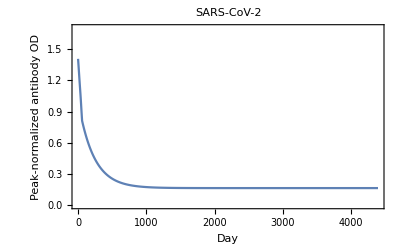

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

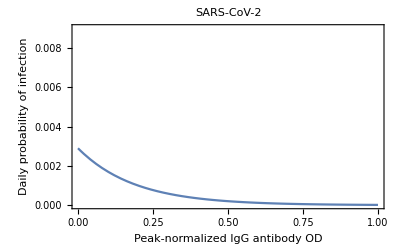

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999998,0.999996,0.999995,0.999993,0.99999,0.999988,0.999986,0.999983,0.999981,0.999978,0.999975,0.999972,0.999969,0.999966,0.999962,0.999958,0.999954,0.99995,0.999946,0.999941,0.999936,0.999931,0.999926,0.99992,0.999914,0.999908,0.999901,0.999894,0.999886,0.999879,0.999871,0.999862,0.999853,0.999844,0.999834,0.999823,0.999812,0.9998,0.999788,0.999775,0.999761,0.999746,0.999731,0.999714,0.999697,0.999678,0.999658,0.999637,0.999615,0.999592,0.999567,0.99954,0.999512,0.999483,0.999452,0.999419,0.999384,0.999347,0.999309,0.999269,0.99923,0.999189,0.999148,0.999106,0.999064,0.999021,0.998977,0.998933,0.998888,0.998842,0.998796,0.998749,0.998701,0.998653,0.998604,0.998554,0.998503,0.998452,0.9984,0.998348,0.998294,0.99824,0.998185,0.99813,0.998073,0.998016,0.997958,0.9979,0.99784,0.99778,0.997719,0.997657,0.997594,0.99753,0.997466,0.997401,0.997335,0.997268,0.9972,0.997131,0.997062,0.996991,0.99692,0.996848,0.996775,0.9967,0.996626,0.99655,0.996473,0.996395,0.996316,0.996237,0.996156,0.996074,0.995992,0.995908,0.995824,0.995738,0.995651,0.995564,0.995475,0.995386,0.995295,0.995203,0.995111,0.995017,0.994922,0.994826,0.994729,0.994631,0.994532,0.994431,0.99433,0.994227,0.994124,0.994019,0.993913,0.993806,0.993698,0.993589,0.993478,0.993366,0.993254,0.99314,0.993024,0.992908,0.99279,0.992672,0.992552,0.99243,0.992308,0.992184,0.992059,0.991933,0.991806,0.991677,0.991547,0.991416,0.991283,0.991149,0.991014,0.990878,0.99074,0.990601,0.99046,0.990319,0.990176,0.990031,0.989886,0.989739,0.98959,0.98944,0.989289,0.989137,0.988983,0.988827,0.988671,0.988513,0.988353,0.988192,0.98803,0.987866,0.987701,0.987534,0.987366,0.987197,0.987026,0.986853,0.98668,0.986504,0.986327,0.986149,0.985969,0.985788,0.985605,0.985421,0.985235,0.985048,0.984859,0.984669,0.984477,0.984284,0.984089,0.983893,0.983695,0.983495,0.983294,0.983092,0.982887,0.982682,0.982474,0.982266,0.982055,0.981843,0.981629,0.981414,0.981197,0.980979,0.980759,0.980537,0.980314,0.980089,0.979863,0.979635,0.979405,0.979174,0.978941,0.978706,0.97847,0.978232,0.977992,0.977751,0.977508,0.977264,0.977018,0.97677,0.97652,0.976269,0.976016,0.975762,0.975506,0.975248,0.974988,0.974727,0.974464,0.974199,0.973933,0.973665,0.973395,0.973124,0.972851,0.972576,0.9723,0.972021,0.971741,0.97146,0.971176,0.970891,0.970604,0.970316,0.970026,0.969734,0.96944,0.969145,0.968847,0.968548,0.968248,0.967945,0.967641,0.967336,0.967028,0.966719,0.966408,0.966095,0.96578,0.965464,0.965146,0.964826,0.964505,0.964182,0.963857,0.96353,0.963202,0.962871,0.962539,0.962206,0.96187,0.961533,0.961194,0.960854,0.960511,0.960167,0.959821,0.959473,0.959124,0.958773,0.95842,0.958065,0.957709,0.957351,0.956991,0.956629,0.956266,0.955901,0.955534,0.955165,0.954795,0.954423,0.954049,0.953674,0.953297,0.952918,0.952537,0.952154,0.95177,0.951384,0.950997,0.950607,0.950216,0.949824,0.949429,0.949033,0.948635,0.948235,0.947834,0.947431,0.947026,0.946619,0.946211,0.945801,0.94539,0.944976,0.944561,0.944145,0.943726,0.943306,0.942885,0.942461,0.942036,0.941609,0.941181,0.94075,0.940319,0.939885,0.93945,0.939013,0.938575,0.938135,0.937693,0.937249,0.936804,0.936357,0.935909,0.935459,0.935007,0.934554,0.934099,0.933643,0.933185,0.932725,0.932263,0.9318,0.931336,0.930869,0.930402,0.929932,0.929461,0.928989,0.928514,0.928039,0.927561,0.927082,0.926602,0.92612,0.925636,0.925151,0.924664,0.924176,0.923686,0.923195,0.922702,0.922207,0.921711,0.921214,0.920715,0.920214,0.919712,0.919208,0.918703,0.918197,0.917689,0.917179,0.916668,0.916156,0.915642,0.915126,0.914609,0.914091,0.913571,0.913049,0.912527,0.912002,0.911477,0.91095,0.910421,0.909891,0.90936,0.908827,0.908293,0.907757,0.90722,0.906682,0.906142,0.905601,0.905058,0.904514,0.903969,0.903422,0.902874,0.902325,0.901774,0.901222,0.900669,0.900114,0.899558,0.899001,0.898442,0.897882,0.897321,0.896758,0.896194,0.895629,0.895062,0.894494,0.893925,0.893355,0.892783,0.892211,0.891637,0.891061,0.890485,0.889907,0.889328,0.888748,0.888166,0.887583,0.886999,0.886414,0.885828,0.885241,0.884652,0.884062,0.883471,0.882879,0.882285,0.881691,0.881095,0.880498,0.8799,0.879301,0.878701,0.8781,0.877497,0.876894,0.876289,0.875683,0.875077,0.874469,0.87386,0.873249,0.872638,0.872026,0.871413,0.870798,0.870183,0.869567,0.868949,0.868331,0.867711,0.867091,0.866469,0.865847,0.865223,0.864599,0.863973,0.863347,0.862719,0.862091,0.861461,0.860831,0.8602,0.859567,0.858934,0.8583,0.857665,0.857029,0.856392,0.855754,0.855116,0.854476,0.853836,0.853194,0.852552,0.851909,0.851265,0.85062,0.849974,0.849328,0.84868,0.848032,0.847383,0.846733,0.846082,0.845431,0.844778,0.844125,0.843471,0.842816,0.842161,0.841504,0.840847,0.840189,0.839531,0.838871,0.838211,0.83755,0.836889,0.836226,0.835563,0.834899,0.834235,0.83357,0.832904,0.832237,0.83157,0.830902,0.830233,0.829564,0.828893,0.828223,0.827551,0.826879,0.826207,0.825533,0.824859,0.824185,0.82351,0.822834,0.822157,0.82148,0.820802,0.820124,0.819445,0.818766,0.818086,0.817405,0.816724,0.816042,0.81536,0.814677,0.813994,0.81331,0.812625,0.81194,0.811255,0.810569,0.809882,0.809195,0.808508,0.80782,0.807131,0.806442,0.805752,0.805062,0.804372,0.803681,0.802989,0.802298,0.801605,0.800913,0.800219,0.799526,0.798832,0.798137,0.797442,0.796747,0.796051,0.795355,0.794658,0.793962,0.793264,0.792567,0.791868,0.79117,0.790471,0.789772,0.789072,0.788373,0.787672,0.786972,0.786271,0.78557,0.784868,0.784166,0.783464,0.782761,0.782058,0.781355,0.780652,0.779948,0.779244,0.77854,0.777835,0.77713,0.776425,0.77572,0.775014,0.774308,0.773602,0.772896,0.772189,0.771482,0.770775,0.770068,0.76936,0.768652,0.767944,0.767236,0.766528,0.765819,0.76511,0.764401,0.763692,0.762983,0.762273,0.761564,0.760854,0.760144,0.759434,0.758723,0.758013,0.757302,0.756591,0.75588,0.755169,0.754458,0.753747,0.753035,0.752324,0.751612,0.7509,0.750188,0.749477,0.748764,0.748052,0.74734,0.746628,0.745915,0.745203,0.74449,0.743778,0.743065,0.742352,0.74164,0.740927,0.740214,0.739501,0.738788,0.738075,0.737362,0.736649,0.735936,0.735223,0.73451,0.733796,0.733083,0.73237,0.731657,0.730944,0.730231,0.729518,0.728805,0.728091,0.727378,0.726665,0.725952,0.725239,0.724527,0.723814,0.723101,0.722388,0.721675,0.720963,0.72025,0.719537,0.718825,0.718112,0.7174,0.716688,0.715976,0.715264,0.714551,0.71384,0.713128,0.712416,0.711704,0.710993,0.710281,0.70957,0.708859,0.708148,0.707437,0.706726,0.706015,0.705304,0.704594,0.703884,0.703173,0.702463,0.701753,0.701044,0.700334,0.699625,0.698915,0.698206,0.697497,0.696788,0.69608,0.695371,0.694663,0.693955,0.693247,0.692539,0.691831,0.691124,0.690417,0.68971,0.689003,0.688296,0.68759,0.686884,0.686178,0.685472,0.684767,0.684061,0.683356,0.682651,0.681947,0.681242,0.680538,0.679834,0.67913,0.678427,0.677723,0.67702,0.676318,0.675615,0.674913,0.674211,0.673509,0.672808,0.672106,0.671405,0.670705,0.670004,0.669304,0.668604,0.667905,0.667205,0.666506,0.665807,0.665109,0.664411,0.663713,0.663015,0.662318,0.661621,0.660924,0.660228,0.659532,0.658836,0.65814,0.657445,0.65675,0.656056,0.655361,0.654667,0.653974,0.653281,0.652588,0.651895,0.651203,0.650511,0.649819,0.649128,0.648437,0.647746,0.647056,0.646366,0.645677,0.644987,0.644298,0.64361,0.642922,0.642234,0.641546,0.640859,0.640173,0.639486,0.6388,0.638115,0.637429,0.636744,0.63606,0.635376,0.634692,0.634009,0.633326,0.632643,0.631961,0.631279,0.630597,0.629916,0.629235,0.628555,0.627875,0.627196,0.626517,0.625838,0.62516,0.624482,0.623804,0.623127,0.62245,0.621774,0.621098,0.620423,0.619748,0.619073,0.618399,0.617725,0.617051,0.616379,0.615706,0.615034,0.614362,0.613691,0.61302,0.61235,0.61168,0.61101,0.610341,0.609672,0.609004,0.608336,0.607669,0.607002,0.606335,0.605669,0.605004,0.604338,0.603674,0.603009,0.602346,0.601682,0.601019,0.600357,0.599695,0.599033,0.598372,0.597712,0.597051,0.596392,0.595732,0.595074,0.594415,0.593757,0.5931,0.592443,0.591787,0.591131,0.590475,0.58982,0.589165,0.588511,0.587858,0.587205,0.586552,0.5859,0.585248,0.584597,0.583946,0.583296,0.582646,0.581996,0.581348,0.580699,0.580051,0.579404,0.578757,0.578111,0.577465,0.576819,0.576175,0.57553,0.574886,0.574243,0.5736,0.572957,0.572315,0.571674,0.571033,0.570393,0.569753,0.569113,0.568474,0.567836,0.567198,0.56656,0.565924,0.565287,0.564651,0.564016,0.563381,0.562747,0.562113,0.561479,0.560846,0.560214,0.559582,0.558951,0.55832,0.55769,0.55706,0.556431,0.555802,0.555174,0.554546,0.553919,0.553292,0.552666,0.552041,0.551416,0.550791,0.550167,0.549543,0.54892,0.548298,0.547676,0.547055,0.546434,0.545813,0.545193,0.544574,0.543955,0.543337,0.542719,0.542102,0.541485,0.540869,0.540254,0.539639,0.539024,0.53841,0.537797,0.537184,0.536571,0.535959,0.535348,0.534737,0.534127,0.533517,0.532908,0.532299,0.531691,0.531084,0.530477,0.52987,0.529264,0.528659,0.528054,0.52745,0.526846,0.526243,0.52564,0.525038,0.524436,0.523835,0.523234,0.522634,0.522035,0.521436,0.520838,0.52024,0.519643,0.519046,0.51845,0.517854,0.517259,0.516664,0.51607,0.515477,0.514884,0.514292,0.5137,0.513108,0.512518,0.511928,0.511338,0.510749,0.51016,0.509572,0.508985,0.508398,0.507812,0.507226,0.506641,0.506056,0.505472,0.504888,0.504305,0.503723,0.503141,0.50256,0.501979,0.501398,0.500819,0.50024,0.499661,0.499083,0.498505,0.497928,0.497352,0.496776,0.496201,0.495626,0.495052,0.494478,0.493905,0.493333,0.492761,0.492189,0.491618,0.491048,0.490478,0.489909,0.48934,0.488772,0.488205,0.487638,0.487071,0.486505,0.48594,0.485375,0.484811,0.484247,0.483684,0.483122,0.48256,0.481998,0.481437,0.480877,0.480317,0.479758,0.479199,0.478641,0.478084,0.477527,0.47697,0.476414,0.475859,0.475304,0.47475,0.474196,0.473643,0.473091,0.472538,0.471987,0.471436,0.470886,0.470336,0.469787,0.469238,0.46869,0.468142,0.467595,0.467049,0.466503,0.465957,0.465412,0.464868,0.464324,0.463781,0.463239,0.462697,0.462155,0.461614,0.461074,0.460534,0.459995,0.459456,0.458918,0.45838,0.457843,0.457306,0.45677,0.456235,0.4557,0.455166,0.454632,0.454099,0.453566,0.453034,0.452502,0.451971,0.451441,0.450911,0.450381,0.449852,0.449324,0.448796,0.448269,0.447743,0.447217,0.446691,0.446166,0.445642,0.445118,0.444594,0.444071,0.443549,0.443028,0.442506,0.441986,0.441466,0.440946,0.440427,0.439909,0.439391,0.438873,0.438357,0.43784,0.437325,0.43681,0.436295,0.435781,0.435267,0.434754,0.434242,0.43373,0.433219,0.432708,0.432198,0.431688,0.431179,0.43067,0.430162,0.429654,0.429147,0.428641,0.428135,0.42763,0.427125,0.42662,0.426117,0.425613,0.425111,0.424609,0.424107,0.423606,0.423105,0.422605,0.422106,0.421607,0.421108,0.420611,0.420113,0.419616,0.41912,0.418625,0.418129,0.417635,0.417141,0.416647,0.416154,0.415661,0.415169,0.414678,0.414187,0.413697,0.413207,0.412718,0.412229,0.411741,0.411253,0.410766,0.410279,0.409793,0.409307,0.408822,0.408338,0.407854,0.40737,0.406887,0.406405,0.405923,0.405441,0.404961,0.40448,0.404001,0.403521,0.403043,0.402564,0.402087,0.401609,0.401133,0.400657,0.400181,0.399706,0.399231,0.398757,0.398284,0.397811,0.397338,0.396867,0.396395,0.395924,0.395454,0.394984,0.394515,0.394046,0.393578,0.39311,0.392642,0.392176,0.39171,0.391244,0.390779,0.390314,0.38985,0.389386,0.388923,0.38846,0.387998,0.387537,0.387076,0.386615,0.386155,0.385695,0.385236,0.384778,0.38432,0.383862,0.383405,0.382949,0.382493,0.382037,0.381582,0.381128,0.380674,0.380221,0.379768,0.379315,0.378863,0.378412,0.377961,0.377511,0.377061,0.376612,0.376163,0.375714,0.375266,0.374819,0.374372,0.373926,0.37348,0.373035,0.37259,0.372146,0.371702,0.371258,0.370815,0.370373,0.369931,0.36949,0.369049,0.368609,0.368169,0.367729,0.367291,0.366852,0.366414,0.365977,0.36554,0.365104,0.364668,0.364232,0.363798,0.363363,0.362929,0.362496,0.362063,0.36163,0.361198,0.360767,0.360336,0.359905,0.359475,0.359046,0.358617,0.358188,0.35776,0.357333,0.356906,0.356479,0.356053,0.355627,0.355202,0.354778,0.354354,0.35393,0.353507,0.353084,0.352662,0.35224,0.351819,0.351398,0.350978,0.350558,0.350138,0.34972,0.349301,0.348883,0.348466,0.348049,0.347632,0.347216,0.346801,0.346386,0.345971,0.345557,0.345144,0.34473,0.344318,0.343906,0.343494,0.343083,0.342672,0.342262,0.341852,0.341442,0.341033,0.340625,0.340217,0.33981,0.339403,0.338996,0.33859,0.338184,0.337779,0.337374,0.33697,0.336567,0.336163,0.33576,0.335358,0.334956,0.334555,0.334154,0.333753,0.333353,0.332954,0.332555,0.332156,0.331758,0.33136,0.330963,0.330566,0.33017,0.329774,0.329378,0.328983,0.328589,0.328195,0.327801,0.327408,0.327015,0.326623,0.326231,0.32584,0.325449,0.325059,0.324669,0.324279,0.32389,0.323501,0.323113,0.322725,0.322338,0.321951,0.321565,0.321179,0.320794,0.320409,0.320024,0.31964,0.319256,0.318873,0.31849,0.318108,0.317726,0.317345,0.316963,0.316583,0.316203,0.315823,0.315444,0.315065,0.314687,0.314309,0.313931,0.313554,0.313178,0.312802,0.312426,0.312051,0.311676,0.311301,0.310927,0.310554,0.310181,0.309808,0.309436,0.309064,0.308693,0.308322,0.307951,0.307581,0.307212,0.306842,0.306474,0.306105,0.305737,0.30537,0.305003,0.304636,0.30427,0.303904,0.303539,0.303174,0.30281,0.302446,0.302082,0.301719,0.301356,0.300994,0.300632,0.30027,0.299909,0.299549,0.299188,0.298829,0.298469,0.29811,0.297752,0.297394,0.297036,0.296679,0.296322,0.295965,0.295609,0.295254,0.294899,0.294544,0.29419,0.293836,0.293482,0.293129,0.292776,0.292424,0.292072,0.291721,0.29137,0.291019,0.290669,0.290319,0.28997,0.289621,0.289272,0.288924,0.288577,0.288229,0.287882,0.287536,0.28719,0.286844,0.286499,0.286154,0.285809,0.285465,0.285122,0.284778,0.284436,0.284093,0.283751,0.28341,0.283068,0.282727,0.282387,0.282047,0.281707,0.281368,0.281029,0.280691,0.280353,0.280015,0.279678,0.279341,0.279005,0.278669,0.278333,0.277998,0.277663,0.277329,0.276995,0.276661,0.276328,0.275995,0.275662,0.27533,0.274999,0.274667,0.274336,0.274006,0.273676,0.273346,0.273017,0.272688,0.272359,0.272031,0.271703,0.271376,0.271049,0.270722,0.270396,0.27007,0.269745,0.26942,0.269095,0.268771,0.268447,0.268123,0.2678,0.267477,0.267155,0.266833,0.266511,0.26619,0.265869,0.265549,0.265229,0.264909,0.26459,0.264271,0.263952,0.263634,0.263316,0.262999,0.262682,0.262365,0.262049,0.261733,0.261417,0.261102,0.260787,0.260473,0.260159,0.259845,0.259532,0.259219,0.258906,0.258594,0.258282,0.257971,0.25766,0.257349,0.257039,0.256729,0.256419,0.25611,0.255801,0.255492,0.255184,0.254876,0.254569,0.254262,0.253955,0.253649,0.253343,0.253037,0.252732,0.252427,0.252123,0.251819,0.251515,0.251211,0.250908,0.250606,0.250303,0.250001,0.2497,0.249399,0.249098,0.248797,0.248497,0.248197,0.247898,0.247599,0.2473,0.247001,0.246703,0.246406,0.246108,0.245811,0.245515,0.245219,0.244923,0.244627,0.244332,0.244037,0.243743,0.243448,0.243155,0.242861,0.242568,0.242275,0.241983,0.241691,0.241399,0.241108,0.240817,0.240526,0.240236,0.239946,0.239656,0.239367,0.239078,0.23879,0.238501,0.238213,0.237926,0.237639,0.237352,0.237065,0.236779,0.236493,0.236208,0.235923,0.235638,0.235353,0.235069,0.234786,0.234502,0.234219,0.233936,0.233654,0.233372,0.23309,0.232808,0.232527,0.232247,0.231966,0.231686,0.231406,0.231127,0.230848,0.230569,0.230291,0.230013,0.229735,0.229458,0.22918,0.228904,0.228627,0.228351,0.228075,0.2278,0.227525,0.22725,0.226976,0.226702,0.226428,0.226154,0.225881,0.225608,0.225336,0.225064,0.224792,0.224521,0.224249,0.223979,0.223708,0.223438,0.223168,0.222898,0.222629,0.22236,0.222092,0.221823,0.221556,0.221288,0.221021,0.220754,0.220487,0.220221,0.219955,0.219689,0.219424,0.219158,0.218894,0.218629,0.218365,0.218101,0.217838,0.217575,0.217312,0.217049,0.216787,0.216525,0.216264,0.216002,0.215741,0.215481,0.21522,0.21496,0.214701,0.214441,0.214182,0.213923,0.213665,0.213407,0.213149,0.212891,0.212634,0.212377,0.212121,0.211864,0.211608,0.211353,0.211097,0.210842,0.210588,0.210333,0.210079,0.209825,0.209571,0.209318,0.209065,0.208813,0.20856,0.208308,0.208057,0.207805,0.207554,0.207303,0.207053,0.206802,0.206553,0.206303,0.206054,0.205805,0.205556,0.205307,0.205059,0.204812,0.204564,0.204317,0.20407,0.203823,0.203577,0.203331,0.203085,0.20284,0.202594,0.20235,0.202105,0.201861,0.201617,0.201373,0.20113,0.200887,0.200644,0.200401,0.200159,0.199917,0.199675,0.199434,0.199193,0.198952,0.198712,0.198472,0.198232,0.197992,0.197753,0.197514,0.197275,0.197036,0.196798,0.19656,0.196323,0.196085,0.195848,0.195612,0.195375,0.195139,0.194903,0.194667,0.194432,0.194197,0.193962,0.193728,0.193494,0.19326,0.193026,0.192793,0.19256,0.192327,0.192094,0.191862,0.19163,0.191398,0.191167,0.190936,0.190705,0.190475,0.190244,0.190014,0.189785,0.189555,0.189326,0.189097,0.188868,0.18864,0.188412,0.188184,0.187957,0.187729,0.187502,0.187276,0.187049,0.186823,0.186597,0.186372,0.186146,0.185921,0.185696,0.185472,0.185247,0.185023,0.1848,0.184576,0.184353,0.18413,0.183908,0.183685,0.183463,0.183241,0.18302,0.182798,0.182577,0.182356,0.182136,0.181916,0.181696,0.181476,0.181257,0.181037,0.180818,0.1806,0.180381,0.180163,0.179945,0.179728,0.17951,0.179293,0.179077,0.17886,0.178644,0.178428,0.178212,0.177996,0.177781,0.177566,0.177351,0.177137,0.176923,0.176709,0.176495,0.176282,0.176068,0.175855,0.175643,0.17543,0.175218,0.175006,0.174795,0.174583,0.174372,0.174161,0.17395,0.17374,0.17353,0.17332,0.17311,0.172901,0.172692,0.172483,0.172274,0.172066,0.171858,0.17165,0.171443,0.171235,0.171028,0.170821,0.170615,0.170408,0.170202,0.169996,0.169791,0.169585,0.16938,0.169175,0.168971,0.168766,0.168562,0.168358,0.168155,0.167951,0.167748,0.167545,0.167342,0.16714,0.166938,0.166736,0.166534,0.166333,0.166132,0.165931,0.16573,0.165529,0.165329,0.165129,0.16493,0.16473,0.164531,0.164332,0.164133,0.163934,0.163736,0.163538,0.16334,0.163143,0.162945,0.162748,0.162551,0.162355,0.162158,0.161962,0.161766,0.16157,0.161375,0.16118,0.160985,0.16079,0.160596,0.160401,0.160207,0.160013,0.15982,0.159627,0.159433,0.159241,0.159048,0.158856,0.158663,0.158471,0.15828,0.158088,0.157897,0.157706,0.157515,0.157325,0.157134,0.156944,0.156754,0.156565,0.156375,0.156186,0.155997,0.155808,0.15562,0.155432,0.155244,0.155056,0.154868,0.154681,0.154494,0.154307,0.15412,0.153934,0.153747,0.153561,0.153376,0.15319,0.153005,0.15282,0.152635,0.15245,0.152266,0.152081,0.151897,0.151714,0.15153,0.151347,0.151164,0.150981,0.150798,0.150616,0.150433,0.150251,0.15007,0.149888,0.149707,0.149525,0.149345,0.149164,0.148983,0.148803,0.148623,0.148443,0.148264,0.148084,0.147905,0.147726,0.147547,0.147369,0.147191,0.147012,0.146835,0.146657,0.146479,0.146302,0.146125,0.145948,0.145772,0.145595,0.145419,0.145243,0.145068,0.144892,0.144717,0.144542,0.144367,0.144192,0.144018,0.143843,0.143669,0.143495,0.143322,0.143148,0.142975,0.142802,0.142629,0.142457,0.142284,0.142112,0.14194,0.141769,0.141597,0.141426,0.141255,0.141084,0.140913,0.140742,0.140572,0.140402,0.140232,0.140062,0.139893,0.139724,0.139555,0.139386,0.139217,0.139049,0.13888,0.138712,0.138544,0.138377,0.138209,0.138042,0.137875,0.137708,0.137542,0.137375,0.137209,0.137043,0.136877,0.136711,0.136546,0.136381,0.136216,0.136051,0.135886,0.135722,0.135558,0.135394,0.13523,0.135066,0.134903,0.134739,0.134576,0.134414,0.134251,0.134088,0.133926,0.133764,0.133602,0.133441,0.133279,0.133118,0.132957,0.132796,0.132635,0.132475,0.132314,0.132154,0.131994,0.131834,0.131675,0.131516,0.131356,0.131198,0.131039,0.13088,0.130722,0.130564,0.130406,0.130248,0.13009,0.129933,0.129775,0.129618,0.129462,0.129305,0.129148,0.128992,0.128836,0.12868,0.128524,0.128369,0.128214,0.128058,0.127903,0.127749,0.127594,0.12744,0.127285,0.127131,0.126977,0.126824,0.12667,0.126517,0.126364,0.126211,0.126058,0.125906,0.125753,0.125601,0.125449,0.125297,0.125146,0.124994,0.124843,0.124692,0.124541,0.12439,0.12424,0.124089,0.123939,0.123789,0.123639,0.12349,0.12334,0.123191,0.123042,0.122893,0.122744,0.122596,0.122447,0.122299,0.122151,0.122003,0.121856,0.121708,0.121561,0.121414,0.121267,0.12112,0.120974,0.120827,0.120681,0.120535,0.120389,0.120243,0.120098,0.119952,0.119807,0.119662,0.119517,0.119373,0.119228,0.119084,0.11894,0.118796,0.118652,0.118509,0.118365,0.118222,0.118079,0.117936,0.117793,0.117651,0.117508,0.117366,0.117224,0.117082,0.11694,0.116799,0.116657,0.116516,0.116375,0.116234,0.116094,0.115953,0.115813,0.115673,0.115533,0.115393,0.115253,0.115114,0.114974,0.114835,0.114696,0.114557,0.114419,0.11428,0.114142,0.114004,0.113866,0.113728,0.11359,0.113453,0.113316,0.113178,0.113042,0.112905,0.112768,0.112632,0.112495,0.112359,0.112223,0.112087,0.111952,0.111816,0.111681,0.111546,0.111411,0.111276,0.111141,0.111007,0.110872,0.110738,0.110604,0.11047,0.110336,0.110203,0.11007,0.109936,0.109803,0.10967,0.109538,0.109405,0.109273,0.10914,0.109008,0.108876,0.108745,0.108613,0.108481,0.10835,0.108219,0.108088,0.107957,0.107827,0.107696,0.107566,0.107436,0.107305,0.107176,0.107046,0.106916,0.106787,0.106658,0.106529,0.1064,0.106271,0.106142,0.106014,0.105885,0.105757,0.105629,0.105501,0.105374,0.105246,0.105119,0.104992,0.104864,0.104738,0.104611,0.104484,0.104358,0.104231,0.104105,0.103979,0.103853,0.103728,0.103602,0.103477,0.103352,0.103226,0.103101,0.102977,0.102852,0.102728,0.102603,0.102479,0.102355,0.102231,0.102107,0.101984,0.10186,0.101737,0.101614,0.101491,0.101368,0.101245,0.101123,0.101,0.100878,0.100756,0.100634,0.100512,0.100391,0.100269,0.100148,0.100027,0.0999055,0.0997846,0.0996638,0.0995432,0.0994227,0.0993023,0.0991821,0.0990621,0.0989422,0.0988224,0.0987028,0.0985834,0.098464,0.0983448,0.0982258,0.0981069,0.0979882,0.0978696,0.0977511,0.0976328,0.0975146,0.0973966,0.0972787,0.0971609,0.0970433,0.0969259,0.0968086,0.0966914,0.0965744,0.0964575,0.0963407,0.0962241,0.0961076,0.0959913,0.0958751,0.0957591,0.0956432,0.0955274,0.0954118,0.0952963,0.0951809,0.0950657,0.0949506,0.0948357,0.0947209,0.0946063,0.0944918,0.0943774,0.0942632,0.0941491,0.0940351,0.0939213,0.0938076,0.093694,0.0935806,0.0934674,0.0933542,0.0932412,0.0931284,0.0930156,0.0929031,0.0927906,0.0926783,0.0925661,0.0924541,0.0923422,0.0922304,0.0921187,0.0920072,0.0918959,0.0917846,0.0916735,0.0915626,0.0914518,0.0913411,0.0912305,0.0911201,0.0910098,0.0908996,0.0907896,0.0906797,0.0905699,0.0904603,0.0903508,0.0902414,0.0901322,0.0900231,0.0899141,0.0898053,0.0896966,0.089588,0.0894796,0.0893713,0.0892631,0.0891551,0.0890471,0.0889394,0.0888317,0.0887242,0.0886168,0.0885095,0.0884024,0.0882954,0.0881885,0.0880818,0.0879751,0.0878687,0.0877623,0.0876561,0.08755,0.087444,0.0873381,0.0872324,0.0871268,0.0870214,0.086916,0.0868108,0.0867057,0.0866008,0.086496,0.0863913,0.0862867,0.0861823,0.0860779,0.0859737,0.0858697,0.0857657,0.0856619,0.0855582,0.0854547,0.0853512,0.0852479,0.0851447,0.0850417,0.0849387,0.0848359,0.0847332,0.0846307,0.0845282,0.0844259,0.0843237,0.0842216,0.0841197,0.0840179,0.0839162,0.0838146,0.0837131,0.0836118,0.0835106,0.0834095,0.0833085,0.0832077,0.083107,0.0830064,0.0829059,0.0828056,0.0827053,0.0826052,0.0825052,0.0824054,0.0823056,0.082206,0.0821065,0.0820071,0.0819078,0.0818087,0.0817096,0.0816107,0.081512,0.0814133,0.0813147,0.0812163,0.081118,0.0810198,0.0809217,0.0808238,0.080726,0.0806282,0.0805306,0.0804332,0.0803358,0.0802386,0.0801414,0.0800444,0.0799475,0.0798508,0.0797541,0.0796576,0.0795611,0.0794648,0.0793686,0.0792726,0.0791766,0.0790808,0.078985,0.0788894,0.0787939,0.0786986,0.0786033,0.0785082,0.0784131,0.0783182,0.0782234,0.0781287,0.0780342,0.0779397,0.0778453,0.0777511,0.077657,0.077563,0.0774691,0.0773753,0.0772817,0.0771881,0.0770947,0.0770014,0.0769082,0.0768151,0.0767221,0.0766292,0.0765365,0.0764438,0.0763513,0.0762589,0.0761666,0.0760744,0.0759823,0.0758903,0.0757984,0.0757067,0.075615,0.0755235,0.0754321,0.0753408,0.0752496,0.0751585,0.0750675,0.0749766,0.0748859,0.0747952,0.0747047,0.0746143,0.074524,0.0744337,0.0743436,0.0742537,0.0741638,0.074074,0.0739843,0.0738948,0.0738053,0.073716,0.0736268,0.0735376,0.0734486,0.0733597,0.0732709,0.0731822,0.0730936,0.0730052,0.0729168,0.0728285,0.0727404,0.0726523,0.0725644,0.0724765,0.0723888,0.0723012,0.0722136,0.0721262,0.0720389,0.0719517,0.0718646,0.0717776,0.0716908,0.071604,0.0715173,0.0714307,0.0713443,0.0712579,0.0711716,0.0710855,0.0709994,0.0709135,0.0708277,0.0707419,0.0706563,0.0705708,0.0704853,0.0704,0.0703148,0.0702297,0.0701447,0.0700598,0.069975,0.0698902,0.0698056,0.0697211,0.0696368,0.0695525,0.0694683,0.0693842,0.0693002,0.0692163,0.0691325,0.0690488,0.0689652,0.0688818,0.0687984,0.0687151,0.0686319,0.0685488,0.0684659,0.068383,0.0683002,0.0682175,0.068135,0.0680525,0.0679701,0.0678878,0.0678057,0.0677236,0.0676416,0.0675597,0.0674779,0.0673963,0.0673147,0.0672332,0.0671518,0.0670705,0.0669893,0.0669082,0.0668272,0.0667463,0.0666656,0.0665849,0.0665043,0.0664237,0.0663433,0.066263,0.0661828,0.0661027,0.0660227,0.0659428,0.065863,0.0657832,0.0657036,0.0656241,0.0655446,0.0654653,0.065386,0.0653069,0.0652278,0.0651489,0.06507,0.0649912,0.0649126,0.064834,0.0647555,0.0646771,0.0645988,0.0645206,0.0644425,0.0643645,0.0642866,0.0642088,0.0641311,0.0640534,0.0639759,0.0638985,0.0638211,0.0637439,0.0636667,0.0635896,0.0635127,0.0634358,0.063359,0.0632823,0.0632057,0.0631292,0.0630528,0.0629764,0.0629002,0.0628241,0.062748,0.062672,0.0625962,0.0625204,0.0624447,0.0623691,0.0622936,0.0622182,0.0621429,0.0620677,0.0619926,0.0619175,0.0618426,0.0617677,0.0616929,0.0616183,0.0615437,0.0614692,0.0613948,0.0613204,0.0612462,0.0611721,0.061098,0.0610241,0.0609502,0.0608764,0.0608027,0.0607291,0.0606556,0.0605822,0.0605089,0.0604356,0.0603624,0.0602894,0.0602164,0.0601435,0.0600707,0.059998,0.0599254,0.0598528,0.0597804,0.059708,0.0596357,0.0595635,0.0594914,0.0594194,0.0593475,0.0592757,0.0592039,0.0591322,0.0590607,0.0589892,0.0589178,0.0588464,0.0587752,0.0587041,0.058633,0.058562,0.0584911,0.0584203,0.0583496,0.058279,0.0582084,0.058138,0.0580676,0.0579973,0.0579271,0.057857,0.0577869,0.057717,0.0576471,0.0575773,0.0575076,0.057438,0.0573685,0.057299,0.0572297,0.0571604,0.0570912,0.0570221,0.0569531,0.0568841,0.0568153,0.0567465,0.0566778,0.0566092,0.0565407,0.0564722,0.0564039,0.0563356,0.0562674,0.0561993,0.0561313,0.0560633,0.0559954,0.0559277,0.05586,0.0557923,0.0557248,0.0556573,0.05559,0.0555227,0.0554555,0.0553883,0.0553213,0.0552543,0.0551874,0.0551206,0.0550539,0.0549873,0.0549207,0.0548542,0.0547878,0.0547215,0.0546553,0.0545891,0.054523,0.054457,0.0543911,0.0543253,0.0542595,0.0541938,0.0541282,0.0540627,0.0539972,0.0539319,0.0538666,0.0538014,0.0537363,0.0536712,0.0536062,0.0535413,0.0534765,0.0534118,0.0533471,0.0532826,0.0532181,0.0531536,0.0530893,0.053025,0.0529609,0.0528967,0.0528327,0.0527688,0.0527049,0.0526411,0.0525774,0.0525137,0.0524501,0.0523867,0.0523232,0.0522599,0.0521966,0.0521335,0.0520703,0.0520073,0.0519444,0.0518815,0.0518187,0.0517559,0.0516933,0.0516307,0.0515682,0.0515058,0.0514434,0.0513812,0.051319,0.0512569,0.0511948,0.0511328,0.0510709,0.0510091,0.0509474,0.0508857,0.0508241,0.0507626,0.0507011,0.0506398,0.0505785,0.0505172,0.0504561,0.050395,0.050334,0.0502731,0.0502122,0.0501514,0.0500907,0.0500301,0.0499695,0.049909,0.0498486,0.0497883,0.049728,0.0496678,0.0496077,0.0495476,0.0494877,0.0494277,0.0493679,0.0493082,0.0492485,0.0491888,0.0491293,0.0490698,0.0490104,0.0489511,0.0488918,0.0488327,0.0487735,0.0487145,0.0486555,0.0485966,0.0485378,0.0484791,0.0484204,0.0483618,0.0483032,0.0482447,0.0481863,0.048128,0.0480698,0.0480116,0.0479534,0.0478954,0.0478374,0.0477795,0.0477217,0.0476639,0.0476062,0.0475486,0.047491,0.0474335,0.0473761,0.0473188,0.0472615,0.0472043,0.0471471,0.0470901,0.0470331,0.0469761,0.0469193,0.0468625,0.0468057,0.0467491,0.0466925,0.046636,0.0465795,0.0465231,0.0464668,0.0464106,0.0463544,0.0462983,0.0462422,0.0461862,0.0461303,0.0460745,0.0460187,0.045963,0.0459074,0.0458518,0.0457963,0.0457409,0.0456855,0.0456302,0.0455749,0.0455198,0.0454647,0.0454096,0.0453547,0.0452998,0.0452449,0.0451902,0.0451355,0.0450808,0.0450262,0.0449717,0.0449173,0.0448629,0.0448086,0.0447544,0.0447002,0.0446461,0.044592,0.0445381,0.0444842,0.0444303,0.0443765,0.0443228,0.0442691,0.0442156,0.044162,0.0441086,0.0440552,0.0440019,0.0439486,0.0438954,0.0438423,0.0437892,0.0437362,0.0436832,0.0436303,0.0435775,0.0435248,0.0434721,0.0434195,0.0433669,0.0433144,0.043262,0.0432096,0.0431573,0.0431051,0.0430529,0.0430008,0.0429487,0.0428967,0.0428448,0.0427929,0.0427411,0.0426894,0.0426377,0.0425861,0.0425345,0.0424831,0.0424316,0.0423803,0.042329,0.0422777,0.0422265,0.0421754,0.0421244,0.0420734,0.0420225,0.0419716,0.0419208,0.04187,0.0418193,0.0417687,0.0417182,0.0416677,0.0416172,0.0415668,0.0415165,0.0414663,0.0414161,0.0413659,0.0413159,0.0412659,0.0412159,0.041166,0.0411162,0.0410664,0.0410167,0.040967,0.0409174,0.0408679,0.0408184,0.040769,0.0407197,0.0406704,0.0406212,0.040572,0.0405229,0.0404738,0.0404248,0.0403759,0.040327,0.0402782,0.0402294,0.0401807,0.0401321,0.0400835,0.040035,0.0399865,0.0399381,0.0398898,0.0398415,0.0397933,0.0397451,0.039697,0.0396489,0.0396009,0.039553,0.0395051,0.0394573,0.0394095,0.0393618,0.0393142,0.0392666,0.0392191,0.0391716,0.0391242,0.0390768,0.0390295,0.0389822,0.0389351,0.0388879,0.0388409,0.0387938,0.0387469,0.0387,0.0386531,0.0386063,0.0385596,0.0385129,0.0384663,0.0384197,0.0383732,0.0383268,0.0382804,0.038234,0.0381878,0.0381415,0.0380954,0.0380492,0.0380032,0.0379572,0.0379112,0.0378653,0.0378195,0.0377737,0.037728,0.0376823,0.0376367,0.0375912,0.0375456,0.0375002,0.0374548,0.0374095,0.0373642,0.0373189,0.0372738,0.0372286,0.0371836,0.0371386,0.0370936,0.0370487,0.0370039,0.0369591,0.0369143,0.0368696,0.036825,0.0367804,0.0367359,0.0366914,0.036647,0.0366027,0.0365584,0.0365141,0.0364699,0.0364258,0.0363817,0.0363376,0.0362936,0.0362497,0.0362058,0.036162,0.0361182,0.0360745,0.0360308,0.0359872,0.0359436,0.0359001,0.0358567,0.0358133,0.0357699,0.0357266,0.0356834,0.0356402,0.035597,0.0355539,0.0355109,0.0354679,0.035425,0.0353821,0.0353393,0.0352965,0.0352538,0.0352111,0.0351685,0.0351259,0.0350834,0.0350409,0.0349985,0.0349561,0.0349138,0.0348715,0.0348293,0.0347872,0.034745,0.034703,0.034661,0.034619,0.0345771,0.0345353,0.0344934,0.0344517,0.03441,0.0343683,0.0343267,0.0342852,0.0342437,0.0342022,0.0341608,0.0341195,0.0340782,0.0340369,0.0339957,0.0339546,0.0339135,0.0338724,0.0338314,0.0337904,0.0337495,0.0337087,0.0336679,0.0336271,0.0335864,0.0335458,0.0335052,0.0334646,0.0334241,0.0333836,0.0333432,0.0333028,0.0332625,0.0332223,0.0331821,0.0331419,0.0331018,0.0330617,0.0330217,0.0329817,0.0329418,0.0329019,0.0328621,0.0328223,0.0327826,0.0327429,0.0327032,0.0326637,0.0326241,0.0325846,0.0325452,0.0325058,0.0324664,0.0324271,0.0323879,0.0323487,0.0323095,0.0322704,0.0322313,0.0321923,0.0321533,0.0321144,0.0320755,0.0320367,0.0319979,0.0319592,0.0319205,0.0318819,0.0318433,0.0318047,0.0317662,0.0317278,0.0316894,0.031651,0.0316127,0.0315744,0.0315362,0.031498,0.0314599,0.0314218,0.0313838,0.0313458,0.0313078,0.0312699,0.0312321,0.0311943,0.0311565,0.0311188,0.0310811,0.0310435,0.0310059,0.0309684,0.0309309,0.0308935,0.0308561,0.0308187,0.0307814,0.0307442,0.0307069,0.0306698,0.0306326,0.0305956,0.0305585,0.0305215,0.0304846,0.0304477,0.0304108,0.030374,0.0303372,0.0303005,0.0302638,0.0302272,0.0301906,0.0301541,0.0301176,0.0300811,0.0300447,0.0300083,0.029972,0.0299357,0.0298995,0.0298633,0.0298271,0.029791,0.029755,0.0297189,0.029683,0.029647,0.0296111,0.0295753,0.0295395,0.0295037,0.029468,0.0294324,0.0293967,0.0293611,0.0293256,0.0292901,0.0292546,0.0292192,0.0291839,0.0291485,0.0291132,0.029078,0.0290428,0.0290076,0.0289725,0.0289375,0.0289024,0.0288674,0.0288325,0.0287976,0.0287627,0.0287279,0.0286931,0.0286584,0.0286237,0.0285891,0.0285545,0.0285199,0.0284854,0.0284509,0.0284164,0.028382,0.0283477,0.0283134,0.0282791,0.0282449,0.0282107,0.0281765,0.0281424,0.0281084,0.0280743,0.0280403,0.0280064,0.0279725,0.0279386,0.0279048,0.027871,0.0278373,0.0278036,0.0277699,0.0277363,0.0277028,0.0276692,0.0276357,0.0276023,0.0275689,0.0275355,0.0275021,0.0274689,0.0274356,0.0274024,0.0273692,0.0273361,0.027303,0.02727,0.0272369,0.027204,0.027171,0.0271381,0.0271053,0.0270725,0.0270397,0.027007,0.0269743,0.0269416,0.026909,0.0268764,0.0268439,0.0268114,0.026779,0.0267465,0.0267142,0.0266818,0.0266495,0.0266173,0.026585,0.0265529,0.0265207,0.0264886,0.0264566,0.0264245,0.0263925,0.0263606,0.0263287,0.0262968,0.026265,0.0262332,0.0262014,0.0261697,0.026138,0.0261064,0.0260748,0.0260432,0.0260117,0.0259802,0.0259488,0.0259173,0.025886,0.0258546,0.0258233,0.0257921,0.0257609,0.0257297,0.0256985,0.0256674,0.0256363,0.0256053,0.0255743,0.0255434,0.0255124,0.0254816,0.0254507,0.0254199,0.0253891,0.0253584,0.0253277,0.025297,0.0252664,0.0252358,0.0252053,0.0251748,0.0251443,0.0251139,0.0250835,0.0250531,0.0250228,0.0249925,0.0249622,0.024932,0.0249018,0.0248717,0.0248416,0.0248115,0.0247815,0.0247515,0.0247215,0.0246916,0.0246617,0.0246318,0.024602,0.0245722,0.0245425,0.0245128,0.0244831,0.0244535,0.0244239,0.0243943,0.0243648,0.0243353,0.0243058,0.0242764,0.024247,0.0242177,0.0241883,0.0241591,0.0241298,0.0241006,0.0240714,0.0240423,0.0240132,0.0239841,0.0239551,0.0239261,0.0238971,0.0238682,0.0238393,0.0238104,0.0237816,0.0237528,0.0237241,0.0236954,0.0236667,0.023638,0.0236094,0.0235808,0.0235523,0.0235238,0.0234953,0.0234669,0.0234385,0.0234101,0.0233817,0.0233534,0.0233252,0.0232969,0.0232687,0.0232406,0.0232124,0.0231843,0.0231563,0.0231282,0.0231002,0.0230723,0.0230443,0.0230164,0.0229886,0.0229608,0.022933,0.0229052,0.0228775,0.0228498,0.0228221,0.0227945,0.0227669,0.0227393,0.0227118,0.0226843,0.0226569,0.0226294,0.022602,0.0225747,0.0225474,0.0225201,0.0224928,0.0224656,0.0224384,0.0224112,0.0223841,0.022357,0.0223299,0.0223029,0.0222759,0.0222489,0.022222,0.0221951,0.0221682,0.0221414,0.0221146,0.0220878,0.0220611,0.0220344,0.0220077,0.0219811,0.0219545,0.0219279,0.0219013,0.0218748,0.0218483,0.0218219,0.0217955,0.0217691,0.0217427,0.0217164,0.0216901,0.0216639,0.0216377,0.0216115,0.0215853,0.0215592,0.0215331,0.021507,0.021481,0.021455,0.021429,0.0214031,0.0213771,0.0213513,0.0213254,0.0212996,0.0212738,0.0212481,0.0212223,0.0211967,0.021171,0.0211454,0.0211198,0.0210942,0.0210687,0.0210432,0.0210177,0.0209923,0.0209668,0.0209415,0.0209161,0.0208908,0.0208655,0.0208402,0.020815,0.0207898,0.0207647,0.0207395,0.0207144,0.0206893,0.0206643,0.0206393,0.0206143,0.0205893,0.0205644,0.0205395,0.0205147,0.0204898,0.020465,0.0204402,0.0204155,0.0203908,0.0203661,0.0203414,0.0203168,0.0202922,0.0202677,0.0202431,0.0202186,0.0201942,0.0201697,0.0201453,0.0201209,0.0200965,0.0200722,0.0200479,0.0200237,0.0199994,0.0199752,0.019951,0.0199269,0.0199028,0.0198787,0.0198546,0.0198306,0.0198066,0.0197826,0.0197586,0.0197347,0.0197108,0.019687,0.0196631,0.0196393,0.0196156,0.0195918,0.0195681,0.0195444,0.0195207,0.0194971,0.0194735,0.0194499,0.0194264,0.0194029,0.0193794,0.0193559,0.0193325,0.0193091,0.0192857,0.0192624,0.0192391,0.0192158,0.0191925,0.0191693,0.0191461,0.0191229,0.0190997,0.0190766,0.0190535,0.0190305,0.0190074,0.0189844,0.0189614,0.0189385,0.0189156,0.0188927,0.0188698,0.018847,0.0188241,0.0188014,0.0187786,0.0187559,0.0187332,0.0187105,0.0186878,0.0186652,0.0186426,0.01862,0.0185975,0.018575,0.0185525,0.01853,0.0185076,0.0184852,0.0184628,0.0184405,0.0184182,0.0183959,0.0183736,0.0183514,0.0183291,0.018307,0.0182848,0.0182627,0.0182406,0.0182185,0.0181964,0.0181744,0.0181524,0.0181304,0.0181085,0.0180865,0.0180647,0.0180428,0.0180209,0.0179991,0.0179773,0.0179556,0.0179338,0.0179121,0.0178905,0.0178688,0.0178472,0.0178256,0.017804,0.0177824,0.0177609,0.0177394,0.0177179,0.0176965,0.0176751,0.0176537,0.0176323,0.0176109,0.0175896,0.0175683,0.0175471,0.0175258,0.0175046,0.0174834,0.0174623,0.0174411,0.01742,0.0173989,0.0173779,0.0173568,0.0173358,0.0173148,0.0172939,0.0172729,0.017252,0.0172311,0.0172103,0.0171894,0.0171686,0.0171479,0.0171271,0.0171064,0.0170857,0.017065,0.0170443,0.0170237,0.0170031,0.0169825,0.0169619,0.0169414,0.0169209,0.0169004,0.01688,0.0168595,0.0168391,0.0168187,0.0167984,0.016778,0.0167577,0.0167374,0.0167172,0.0166969,0.0166767,0.0166565,0.0166364,0.0166162,0.0165961,0.016576,0.016556,0.0165359,0.0165159,0.0164959,0.0164759,0.016456,0.0164361,0.0164162,0.0163963,0.0163765,0.0163566,0.0163368,0.0163171,0.0162973,0.0162776,0.0162579,0.0162382,0.0162185,0.0161989,0.0161793,0.0161597,0.0161402,0.0161206,0.0161011,0.0160816,0.0160621,0.0160427,0.0160233,0.0160039,0.0159845,0.0159652,0.0159458,0.0159265,0.0159072,0.015888,0.0158688,0.0158496,0.0158304,0.0158112,0.0157921,0.0157729,0.0157539,0.0157348,0.0157157,0.0156967,0.0156777,0.0156587,0.0156398,0.0156208,0.0156019,0.015583,0.0155642,0.0155453,0.0155265,0.0155077,0.015489,0.0154702,0.0154515,0.0154328,0.0154141,0.0153954,0.0153768,0.0153582,0.0153396,0.015321,0.0153025,0.015284,0.0152654,0.015247,0.0152285,0.0152101,0.0151917,0.0151733,0.0151549,0.0151366,0.0151182,0.0150999,0.0150817,0.0150634,0.0150452,0.015027,0.0150088,0.0149906,0.0149725,0.0149543,0.0149362,0.0149181,0.0149001,0.014882,0.014864,0.014846,0.0148281,0.0148101,0.0147922,0.0147743,0.0147564,0.0147385,0.0147207,0.0147029,0.0146851,0.0146673,0.0146495,0.0146318,0.0146141,0.0145964,0.0145787,0.0145611,0.0145435,0.0145259,0.0145083,0.0144907,0.0144732,0.0144557,0.0144382,0.0144207,0.0144032,0.0143858,0.0143684,0.014351,0.0143336,0.0143163,0.0142989,0.0142816,0.0142643,0.0142471,0.0142298,0.0142126,0.0141954,0.0141782,0.014161,0.0141439,0.0141268,0.0141097,0.0140926,0.0140755,0.0140585,0.0140415,0.0140245,0.0140075,0.0139905,0.0139736,0.0139567,0.0139398,0.0139229,0.0139061,0.0138892,0.0138724,0.0138556,0.0138389,0.0138221,0.0138054,0.0137887,0.013772,0.0137553,0.0137386,0.013722,0.0137054,0.0136888,0.0136722,0.0136557,0.0136392,0.0136226,0.0136062,0.0135897,0.0135732,0.0135568,0.0135404,0.013524,0.0135076,0.0134913,0.0134749,0.0134586,0.0134423,0.0134261,0.0134098,0.0133936,0.0133774,0.0133612,0.013345,0.0133289,0.0133127,0.0132966,0.0132805,0.0132644,0.0132484,0.0132323,0.0132163,0.0132003,0.0131843,0.0131684,0.0131524,0.0131365,0.0131206,0.0131047,0.0130889,0.013073,0.0130572,0.0130414,0.0130256,0.0130098,0.0129941,0.0129784,0.0129626,0.012947,0.0129313,0.0129156,0.0129,0.0128844,0.0128688,0.0128532,0.0128376,0.0128221,0.0128066,0.0127911,0.0127756,0.0127601,0.0127447,0.0127293,0.0127138,0.0126985,0.0126831,0.0126677,0.0126524,0.0126371,0.0126218,0.0126065,0.0125912,0.012576,0.0125608,0.0125456,0.0125304,0.0125152,0.0125001,0.0124849,0.0124698,0.0124547,0.0124397,0.0124246,0.0124096,0.0123945,0.0123795,0.0123645,0.0123496,0.0123346,0.0123197,0.0123048,0.0122899,0.012275,0.0122601,0.0122453,0.0122305,0.0122157,0.0122009,0.0121861,0.0121714,0.0121566,0.0121419,0.0121272,0.0121125,0.0120979,0.0120832,0.0120686,0.012054,0.0120394,0.0120248,0.0120103,0.0119957,0.0119812,0.0119667,0.0119522,0.0119378,0.0119233,0.0119089,0.0118945,0.0118801,0.0118657,0.0118513,0.011837,0.0118226,0.0118083,0.011794,0.0117798,0.0117655,0.0117513,0.011737,0.0117228,0.0117086,0.0116945,0.0116803,0.0116662,0.011652,0.0116379,0.0116238,0.0116098,0.0115957,0.0115817,0.0115677,0.0115537,0.0115397,0.0115257,0.0115118,0.0114978,0.0114839,0.01147,0.0114561,0.0114422,0.0114284,0.0114146,0.0114007,0.0113869,0.0113732,0.0113594,0.0113456,0.0113319,0.0113182,0.0113045,0.0112908,0.0112771,0.0112635,0.0112498,0.0112362,0.0112226,0.011209,0.0111955,0.0111819,0.0111684,0.0111549,0.0111414,0.0111279,0.0111144,0.011101,0.0110875,0.0110741,0.0110607,0.0110473,0.0110339,0.0110206,0.0110072,0.0109939,0.0109806,0.0109673,0.010954,0.0109408,0.0109275,0.0109143,0.0109011,0.0108879,0.0108747,0.0108615,0.0108484,0.0108353,0.0108221,0.010809,0.010796,0.0107829,0.0107698,0.0107568,0.0107438,0.0107308,0.0107178,0.0107048,0.0106918,0.0106789,0.010666,0.0106531,0.0106402,0.0106273,0.0106144,0.0106016,0.0105887,0.0105759,0.0105631,0.0105503,0.0105376,0.0105248,0.0105121,0.0104993,0.0104866,0.0104739,0.0104613,0.0104486,0.0104359,0.0104233,0.0104107,0.0103981,0.0103855,0.0103729,0.0103604,0.0103478,0.0103353,0.0103228,0.0103103,0.0102978,0.0102854,0.0102729,0.0102605,0.0102481,0.0102356,0.0102233,0.0102109,0.0101985,0.0101862,0.0101738,0.0101615,0.0101492,0.0101369,0.0101247,0.0101124,0.0101002,0.0100879,0.0100757,0.0100635,0.0100514,0.0100392,0.010027,0.0100149,0.0100028,0.00999066,0.00997857,0.00996649,0.00995443,0.00994238,0.00993034,0.00991832,0.00990631,0.00989432,0.00988234,0.00987038,0.00985843,0.0098465,0.00983458,0.00982268,0.00981078,0.00979891,0.00978705,0.0097752,0.00976337,0.00975155,0.00973974,0.00972795,0.00971618,0.00970441,0.00969267,0.00968093,0.00966921,0.00965751,0.00964582,0.00963414,0.00962248,0.00961083,0.0095992,0.00958758,0.00957597,0.00956438,0.0095528,0.00954124,0.00952969,0.00951815,0.00950663,0.00949512,0.00948363,0.00947215,0.00946068,0.00944923,0.00943779,0.00942637,0.00941496,0.00940356,0.00939217,0.00938081,0.00936945,0.00935811,0.00934678,0.00933546,0.00932416,0.00931288,0.0093016,0.00929034,0.0092791,0.00926786,0.00925665,0.00924544,0.00923425,0.00922307,0.00921191,0.00920075,0.00918962,0.00917849,0.00916738,0.00915628,0.0091452,0.00913413,0.00912307,0.00911203,0.009101,0.00908998,0.00907898,0.00906799,0.00905701,0.00904605,0.0090351,0.00902416,0.00901323,0.00900232,0.00899143,0.00898054,0.00896967,0.00895881,0.00894797,0.00893714,0.00892632,0.00891551,0.00890472,0.00889394,0.00888317,0.00887242,0.00886168,0.00885095,0.00884024,0.00882954,0.00881885,0.00880817,0.00879751,0.00878686,0.00877622,0.0087656,0.00875499,0.00874439,0.00873381,0.00872323,0.00871267,0.00870213,0.00869159,0.00868107,0.00867056,0.00866007,0.00864958,0.00863911,0.00862866,0.00861821,0.00860778,0.00859758}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

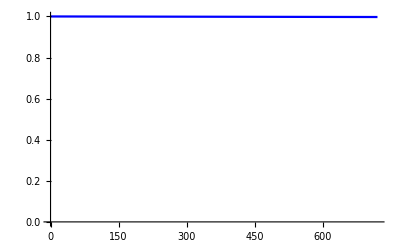

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

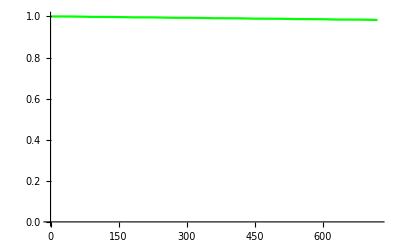

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

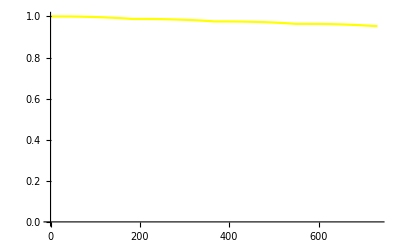

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

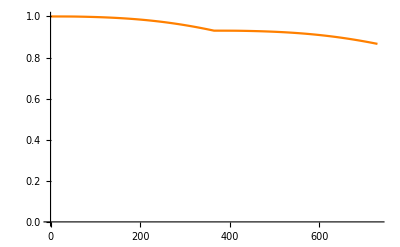

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

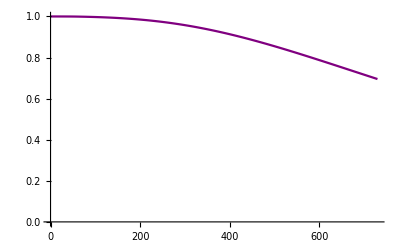

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

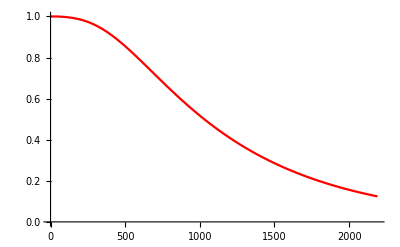

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

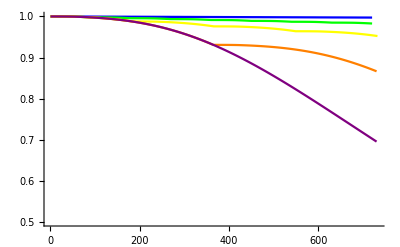

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/immuno_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/immuno_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.304629,0.133482,0.0476591,0.0171491,0.00272072].

Show[0.304629,0.133482,0.0476591,0.0171491,0.00272072]

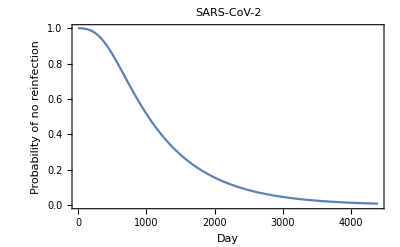

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{320.551,10.685,0.878223}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1029.41,34.3138,2.82031}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2940.5,98.0166,8.05615}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

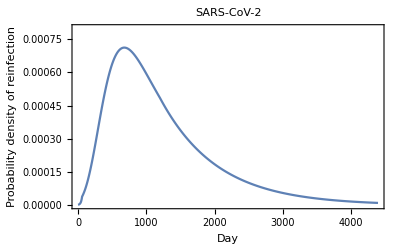

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed